```mathematica
l=1
g=981/100
T=2 Pi Sqrt[l/g]
N[T,15]
```

1

981/100

(20 π)/(3 √109)

2.00606668071065

```mathematica
Pi/2.
```

```mathematica
1.5707963267948966
```

```mathematica
Integrate[E^x,{x,0.,1}]
```

1.71828

```mathematica
f[x_]:=x^7
Integrate[f[x],{x,0,1.}]
```

0.125

```mathematica
Plot[f[x],{x,-1,1}]
```

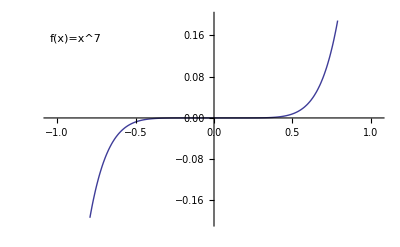

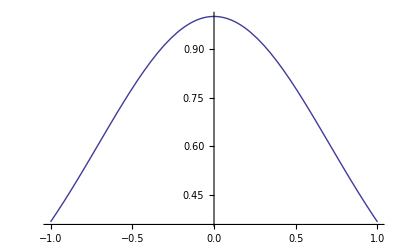

```mathematica
g[x_]:=E^(-x^2)
Plot[g[x],{x,-1,1}]
```

```mathematica
N[Integrate[g[x],{x,0,1}],15]
```

0.746824132812427

```mathematica
N[E,15]
```

2.71828182845905

```mathematica
h[x_]:=x^3/(E^x-1)
```

```mathematica
N[Integrate[h[x],{x,0,Infinity}],15]
```

6.49393940226683

```mathematica
b[x_,y_]:=E^(-x y)
```

```mathematica
a=Integrate[b[x,y],{x,0,2.},{y,0,1}]
```

1.31926

```mathematica
q[x_]:=Sqrt[(1-x^2)(2-x)]
N[Integrate[q[x],{x,-1,1}],15]
```

2.20334573182474

```mathematica
q[x]
```

√((2-x) (1-x^2))

```mathematica
Plot[q[x],{x,-1,1}]
```

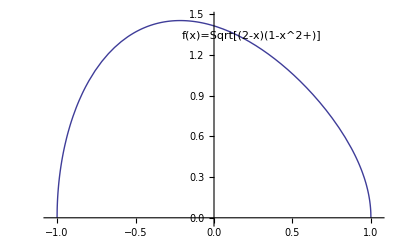

```mathematica
l[x_,y_]:=E^(-x y)
```

```mathematica
N[Integrate[l[x,y],{x,0,2},{y,0,1}],15]
```

1.31926335616954

```mathematica
Plot3D[l[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
1/Sqrt[10000.]
```

0.01

```mathematica
eShift={11.183847,1.407396,19.072715,0.870096}
eActual={11.4,1.2,13.2,0.9}
```

{11.1838,1.4074,19.0727,0.870096}

{11.4,1.2,13.2,0.9}

```mathematica
error=(eShift-eActual)/eActual
```

{-0.0189608,0.17283,0.444903,-0.0332267}

```mathematica
(0.0189+0.1728+0.4490+0.03323)/4
```

0.168483

```mathematica
Abs[error*100]
```

{1.89608,17.283,44.4903,3.32267}